## Setting

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
Needs["ErrorBarPlots`"];

plotparameters=Evaluate[{Frame->True,BaseStyle->{FontSize->16,FontFamily->"Arial",FontColor->Black},LabelStyle->{FontSize->22,FontFamily->"Arial",FontColor->Black}},Axes -> {False, False}, Method->{"OptimizePlotMarkers"->False},FrameStyle->Thickness[0.003]];

SetOptions[Plot,plotparameters];
SetOptions[ListLinePlot,plotparameters];
SetOptions[ListPlot,plotparameters];
SetOptions[ErrorListPlot,plotparameters];
SetOptions[ListContourPlot,plotparameters];
SetOptions[ListLogLogPlot,plotparameters];
SetOptions[ListLogPlot,plotparameters];
SetOptions[Style,SingleLetterItalics->False];
verticalSize=250;
SetDirectory["~/Works/adaptive_potential/distribution/convolution/p1/"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Parameters and functions

```mathematica
A=1;
σ0=1;
L=8;
d=0.4;
density=0.7;
dis=0.01;
τ=0.5;
β=1;
σ1=0.5;
σ2=1.5;
τ1=0.25;
τ2=0.25;
ρ10=1;
ρ20=0.5654856738275738;
ρ1[z_]:=ρ10 Exp[-β A σ0 z];
ρ2[z_]:=ρ20 Exp[(1/2 β A τ z-σ0/τ)^2-σ0^2/τ^2];
ρ3[z_]:=ρ30 (Exp[(1/2 β A τ1 z-σ1/τ1)^2-σ1^2/τ1^2]+Exp[(1/2 β A τ2 z-σ2/τ2)^2-σ2^2/τ2^2]);
p2[σ_]:=Exp[-(σ-σ0)^2/τ^2]
p3[σ_]:=Exp[-(σ-σ1)^2/τ1^2]+Exp[-(σ-σ2)^2/τ2^2]
ϕ[r_,σ_]:=A*σ*r
B21[σ_,c_]:=c*σ^3
B22[σ_,c_]:=c*d^3*(Exp[β*Abs[σ]]-1)
dis=0.001;
tol = 0.001;
den = 0;
```

## ρ_1(r,σ) with second virial expansion coefficient B_2

### initial condition (ideal gas)

```mathematica
(*Normalization: ∫_0^L ρ(z)dz=L/d^3*)
q=0.5;
ρin=1/10;
While[Abs[den-density]>tol,
Do[
ρsideal[z]=q*DiscreteDelta[σ0-σ0]*Exp[-β*(A*σ0*z)];
,{z,0,L,dis}];
data1 =Table[ρsideal[z],{z,0,L,dis}];
den =Total[data1[[All]]]*dis;
q = q * density/ den;
Print[den];
]
```

0.500082

0.7

### B_2(σ) = c̃ d^3[exp(βσ)-1]

```mathematica
c=-3.1;
den = 0;
(*Normalization: ∫_0^L ρ(z)dz=L/d^3*)
While[Abs[den-density]>tol,
Do[
ρs1[z]=ρ/.FindRoot[ρ==q*DiscreteDelta[σ0-σ0]*Exp[-β*(2*B22[σ0,c]*ρ+A*σ0*z)],{ρ,data1[[Round[z*100+1]]]}];
,{z,0,L,dis}];
data2 =Table[{z, ρs1[z]},{z,0,L,dis}];
(*Export["rho_sig_z_b21_c05.txt",data2];*)
(*Do[
Nprofile[σ]=0
,{σ,1,Length[data2[[All,1]]],1}];*)

den = Total[data2[[All,2]]]*dis;
q = q * density/ den;
Print[den];
]
```

0.641987

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

0.739459

0.673542

0.717309

0.688716

0.707338

0.695232

0.703098

0.697988

0.701307

0.699151

```mathematica
Do[
sigzprofile[z] = σ0*Exp[-β*A*σ0*z];
,{z,0,L,dis}]
sigztable = Table[{z,sigzprofile[z]},{z,0,L,dis}];
```

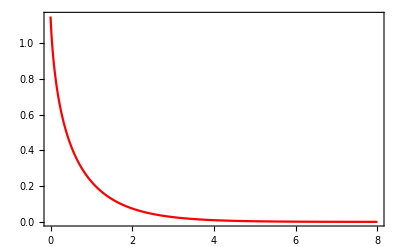

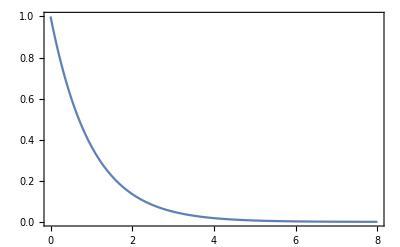

```mathematica
plotb21c05=ListLinePlot[data2,PlotStyle->Red,PlotRange->Full]
plotsigz=ListLinePlot[sigztable,PlotRange->Full]
(*plotNb21c05=ListLinePlot[Table[{σ*dis-4,Nprofile[σ]},{σ,1,Length[data2[[All,1]]],1}],PlotStyle->Red,PlotRange->Full]*)
```

```mathematica
Export["rho_z_b22_c-4.txt",data2];
Export["sig_z_b22_c-4.txt",sigztable];
```